```mathematica
data=Import["../fatal-police-shootings-data.csv"];
```

```mathematica
allDates=data[[2;;, 3]];
dates=Select[allDates,StringStartsQ[#,{"2015","2016","2017","2018"}]&];
counts:=Counts[dates];
days:=365*4+1;
```

```mathematica
categories=KeySort[Append[Counts[Values[counts]], 0->days-Length[counts]]];
n=Max[Keys[categories]];
For[i=1,i<n,i++,If[KeyExistsQ[categories,i],None,categories[i]=0]];
{n,categories}
```

{10,<|0→108,1→287,2→324,3→310,4→227,5→116,6→53,7→21,8→11,9→3,10→1|>}

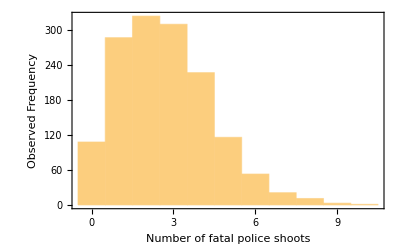

```mathematica
weightedData=WeightedData[Keys[categories],Values[categories]];
fig=Histogram[
weightedData,n,
Frame->{True,True,False,False},
FrameTicks->{Range[0,n],Automatic},
FrameLabel->{"Number of fatal police shoots","Observed Frequency"}
]
Export["q3-all-obs.eps",fig];
```

```mathematica
k=Sum[x*categories[x],{x,Keys[categories]}]/days;
{k,N[k]}
```

{3943/1461,2.69884}

```mathematica
a=Map[Function[x, (ⅇ^-k k^x)/(x!)],Range[0,n-1]];
a=Append[a,1-Accumulate[a][[-1]]];
{N[a],days*N[a]}
a[[-2]]+=a[[-1]];
a=Delete[a,-1];
expect=days*a;
n=Length[expect];
{N[a],N[expect]}
```

{{0.0672838,0.181588,0.245038,0.220439,0.148732,0.0802808,0.0361108,0.0139224,0.0046968,0.00140843,0.000499723},{98.3016,265.3,358.,322.062,217.298,117.29,52.7579,20.3407,6.86203,2.05772,0.730095}}

{{0.0672838,0.181588,0.245038,0.220439,0.148732,0.0802808,0.0361108,0.0139224,0.0046968,0.00190816},{98.3016,265.3,358.,322.062,217.298,117.29,52.7579,20.3407,6.86203,2.78782}}

```mathematica
observe=Values[categories];
observe[[-2]]+=observe[[-1]];
observe=Delete[observe,-1]
```

{108,287,324,310,227,116,53,21,11,4}

```mathematica
X2=∑_(i=1)^n (expect[[i]]-observe[[i]])^2/expect[[i]];
N[X2]
```

9.9049

```mathematica
P=1-CDF[ChiSquareDistribution[n],X2];
N[P]
```

0.448876

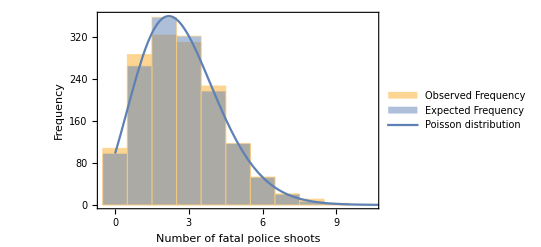

```mathematica
n=Length[observe];
weightedObserveData=WeightedData[Keys[categories],Values[categories]];;
weightedExpectData=WeightedData[Range[0,n-1],expect];
fig=Show[
Histogram[
{Legended[weightedObserveData,"Observed Frequency"],
Legended[weightedExpectData,"Expected Frequency"]},n,
Frame->{True,True,False,False},
FrameTicks->{Range[0,n],Automatic},
FrameLabel->{"Number of fatal police shoots","Frequency"}
],
Plot[
Legended[Evaluate[days*PDF[PoissonDistribution[k],x]],"Poisson distribution"],{x,0,n+1},
PlotStyle->Thick,
PlotLegends->Automatic
]]
Export["q3-all-exp.eps",fig];
```